```mathematica
data=Import["C:\\Users\\Я\\Desktop\\machine-learning-ex6\\ex6\\ex6data1.mat","Data"]
```

{{{1.9643,4.5957},{2.2753,3.8589},{2.9781,4.5651},{2.932,3.5519},{3.5772,2.856},{4.015,3.1937},{3.3814,3.4291},{3.9113,4.1761},{2.7822,4.0431},{2.5518,4.6162},{3.3698,3.9101},{3.1048,3.0709},{1.9182,4.0534},{2.2638,4.3706},{2.6555,3.5008},{3.1855,4.2888},{3.6579,3.8692},{3.9113,3.4291},{3.6002,3.1221},{3.0357,3.3165},{1.5841,3.3575},{2.0103,3.2039},{1.9527,2.7843},{2.2753,2.7127},{2.3099,2.9584},{2.8283,2.6309},{3.0473,2.2931},{2.4827,2.0373},{2.5057,2.3853},{1.8721,2.0577},{2.0103,2.3546},{1.2269,2.3239},{1.8951,2.9174},{1.561,3.0709},{1.5495,2.6923},{1.6878,2.4057},{1.4919,2.0271},{0.962,2.682},{1.1693,2.9276},{0.8122,2.9992},{0.9735,3.3881},{1.25,3.1937},{1.3191,3.5109},{2.2292,2.201},{2.4482,2.6411},{2.7938,1.9656},{2.091,1.6177},{2.5403,2.8867},{0.9044,3.0198},{0.76615,2.5899},{0.086405,4.1045}},{{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{1.}}}

```mathematica
X1=Select[dataᵀ,#[[1]]==0&][[;;,2]];
X2=Select[dataᵀ,#[[1]]==1&][[;;,2]];
X=Table[Prepend[data[[2,i]],1],{i,1,Length[data[[2]]]}];
Y=data[[1]]/.{0.->-1,1.->1};
```

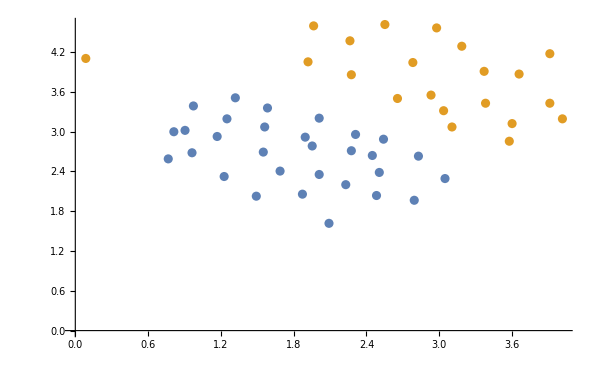

```mathematica
ListPlot[{X1,X2}]
```

```mathematica
M[x_,w_,y_]:=y w.x
L[M_]:=Ramp[-M+1]
Q[w_,C_]:=C Sum[L[M[X[[i]],w,Y[[i]]]],{i,1,Length[X]}]+Sum[w[[i]]^2,{i,2,Length[w]}]
```

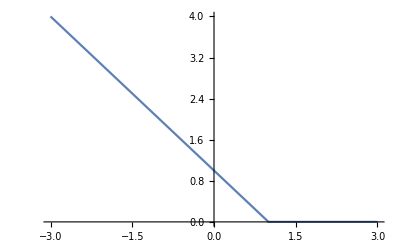

```mathematica
Plot[Ramp[-x+1],{x,-3,3}]
```

```mathematica
w=NArgMin[Q[{w0,w1,w2},1],{w0,w1,w2}]
```

{-8.01813,0.978742,1.75986}

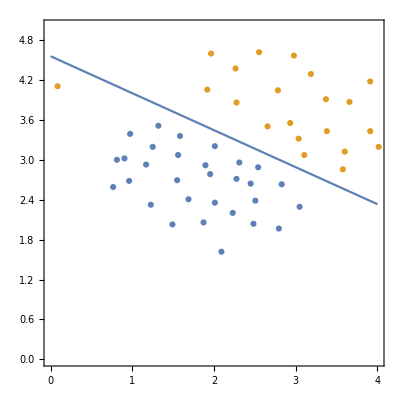

```mathematica
Show[ContourPlot[w.{1,x1,x2}==0,{x1,0,4},{x2,0,5}],ListPlot[{X1,X2}]]
```